```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*.ods"])//TableForm
```

data\t1_t_in_ms_i_in_V_cu005.ods
data\t1_t_in_ms_i_in_V_cu01.ods
data\t1_t_in_ms_i_in_V_cu02.ods
data\t2_CP_tau0k4ms_t_in_ms_i_in_V_cu005.ods
data\t2_CP_tau0k5ms_t_in_ms_i_in_V_cu01.ods
data\t2_CP_tau0k5ms_t_in_ms_i_in_V_cu02.ods
data\t2_MG_tau0k3ms_t_in_ms_i_in_V_cu005.ods
data\t2_MG_tau0k5ms_t_in_ms_i_in_V_cu01.ods
data\t2_MG_tau0k5ms_t_in_ms_i_in_V_cu02.ods
data\t2_spinecho_t_in_ms_i_in_V_cu005.ods
data\t2_spinecho_t_in_ms_i_in_V_cu01.ods
data\t2_spinecho_t_in_ms_i_in_V_cu02.ods
data\t2stern_t_in_mus_i_in_v_cu02.ods
data\t2stern_t_in_mus_i_in_v_mineralol.ods

```mathematica
(t2stoel=First@Import["data/t2stern_t_in_mus_i_in_v_mineralol.ods"])//TableForm;
(t2stcu02=First@Import["data/t2stern_t_in_mus_i_in_v_cu02.ods"])//TableForm;
t1005=First@Import["data/t1_t_in_ms_i_in_V_cu005.ods"];
t101=First@Import["data/t1_t_in_ms_i_in_V_cu01.ods"];
t102=First@Import["data/t1_t_in_ms_i_in_V_cu02.ods"];
spin005={2,1}*#&/@First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu005.ods"];
spin01={2,1}*#&/@First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu01.ods"];
spin02={2,1}*#&/@First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu02.ods"];
mg005=First@Import["data/t2_MG_tau0k3ms_t_in_ms_i_in_V_cu005.ods"];
mg01=First@Import["data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu01.ods"];
mg02=First@Import["data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu02.ods"];
cp005=First@Import["data/t2_CP_tau0k4ms_t_in_ms_i_in_V_cu005.ods"];
cp01=First@Import["data/t2_CP_tau0k5ms_t_in_ms_i_in_V_cu01.ods"];
cp02={-1,0}+#&/@First@Import["data/t2_CP_tau0k5ms_t_in_ms_i_in_V_cu02.ods"];
```

```mathematica
ToErrorForm[{x1_,x2_}]:={(x1+x2)/2,Abs[x2-x1]/2};
applyWithError[fct_,arg_]:=Module[{i,total,direction},
total=0;
(* calculate gauss error *)
direction=Table[0,{i,1,Length[arg]}];
For[i=1,i≤Length[arg],i++,
direction⟦i⟧=1;
total+=(((Derivative@@direction)[fct])@@arg⟦1;;,1⟧)^2*arg⟦i,2⟧^2;
direction⟦i⟧=0;
];
{fct@@arg⟦1;;,1⟧,Sqrt[total]}
]
weightedMean[vals_]:={Sum[vals⟦i,1⟧/vals⟦i,2⟧,{i,1,Length[vals]}]/Sum[1/vals⟦i,2⟧,{i,1,Length[vals]}],Sqrt[1/(Sum[1/vals⟦i,2⟧,{i,1,Length[vals]}])^2]}
<<"ErrorBarPlots`"
```

## T_2^*

{{0.370492,0.0478545},{448.429,28.1648},{0.086246,0.0485313}}

{{0.303188,0.0458959},{433.604,30.2053},{0.0610739,0.050498}}

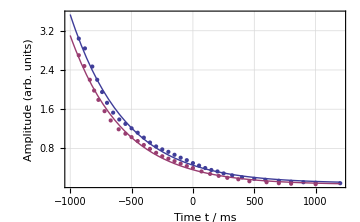

T_2^*

{{448.429,28.1648},{433.604,30.2053}}

{441.275,14.5747}

```mathematica
dats={t2stoel,t2stcu02};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,a* E^(-x/b)+c,{{a,0.5},{b,500},{c,0}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧},{x,-1000,1200}],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
Print["T_2^*"];
t2st=(ToErrorForm/@#["ParameterConfidenceIntervals"]&/@fits)⟦1;;,2⟧
weightedMean[t2st]
```

## T_1

{{-3.99407,0.0435192},{20.4734,0.610638},{1.99772,0.0383346}}

{{-3.97584,0.0370221},{9.63981,0.247873},{1.95093,0.0304129}}

{{-5.26085,0.0474755},{4.24683,0.107315},{2.62475,0.042459}}

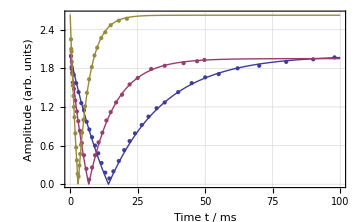

```mathematica
dats={t1005,t101,t102};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,Abs[a* E^(-x/b)+c],{{a,-4},{b,7},{c,2}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,100}],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
t2=(ToErrorForm/@#["ParameterConfidenceIntervals"]&/@fits)⟦1;;,2⟧;
```

## T_2 - Spin Echo

{{2.19272,0.0418653},{22.0102,1.13489},{-0.0965997,0.0488123}}

{{2.0958,0.0318941},{9.84843,0.4723},{0.0280683,0.0358801}}

{{2.76369,0.0277249},{4.41584,0.138031},{0.0291403,0.0281363}}

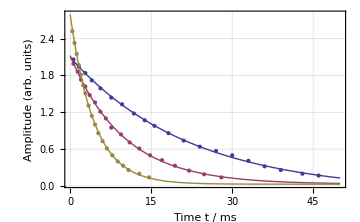

```mathematica
dats={spin005,spin01,spin02};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,a* E^(-x/b)+c,{{a,2},{b,7},{c,0}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,50},PlotRange->All],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
t1se=(ToErrorForm/@#["ParameterConfidenceIntervals"]&/@fits)⟦1;;,2⟧;
```

## T_2 - MG

{{1.89398,0.0081887},{20.1747,0.266894},{0.0981004,0.0095061}}

{{2.08809,0.0289923},{10.1668,0.423914},{0.0112963,0.0335434}}

{{3.35498,0.0725658},{4.49674,0.195569},{0.0397695,0.027642}}

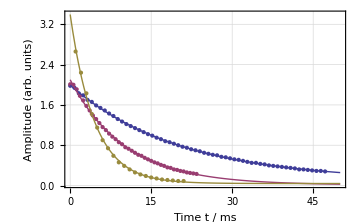

```mathematica
dats={mg005,mg01,mg02};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,a* E^(-x/b)+c,{{a,2},{b,7},{c,0}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,50},PlotRange->All],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
t1mg=(ToErrorForm/@#["ParameterConfidenceIntervals"]&/@fits)⟦1;;,2⟧;
```

## T_2 - CP - obsolete

{{1.86295,0.103574},{8.78842,0.698269},{0.0316697,0.0548157},{7.67763,0.129181},{0.125548,0.0700434},{-4.0169×10^7,0.},{-0.323508,0.0429995}}

{{1.88691,0.253554},{5.87279,0.987763},{0.073612,0.0472455},{5.98507,0.12797},{0.0895698,0.145573},{17.403,119.862},{-0.286157,0.049176}}

{{5.27052,2.10329},{2.56408,0.610151},{0.0905354,0.0633983},{9.13469,1.12776},{-0.0808608,0.257628},{2.79166×10^6,0.},{-0.986385,0.248078}}

{0.999161,0.998966,0.999773}

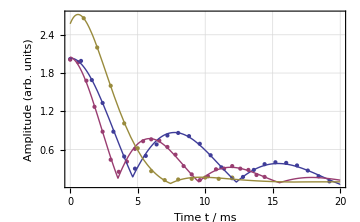

```mathematica
dats={cp005,cp01,cp02};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#1,a* E^(-x/b)*(Abs[Cos[π x/d+g]]+e E^(-x/f))+c,{{a,2},{b,7},{c,0},{d,7},{e,0.2},{f,7},{g,0}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
#["RSquared"]&/@fits
Show[
ListPlot[dats,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,20},PlotRange->{0,4}],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
```

## T_2 + δ - CP

```mathematica
fkt=Abs[x[t]]/.DSolve[{x'[t]==-1/T1 x[t]+ω y[t],y'[t]==-1/T2 y[t]-ω x[t],x[0]==x0,y[0]==y0},{x[t],y[t]},t];
```

{{8.68322,0.869332},{0.408866,0.00683925},{1.78866,0.110988},{0.597633,0.0955516},{0.2406,0.0983941},{0.0783696,0.0535019}}

{{5.50659,0.458343},{0.525038,0.0132408},{1.8543,0.0980674},{0.618708,0.131633},{0.174674,0.0850038},{0.0451066,0.0530615}}

{{2.54387,0.509135},{0.351817,0.0269056},{2.62001,0.0826949},{2.16227,0.813057},{0.0384351,0.0598363},{-0.0871067,0.162667}}

{0.999116,0.998592,0.999798}

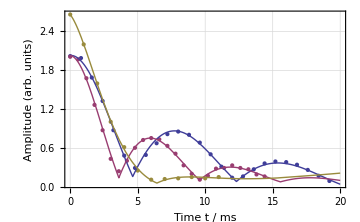

{{8.68322,0.869332},{5.50659,0.458343},{2.54387,0.509135}}

Winkelabweichungen:
 π/2 Puls:

{{18.4756,40.7257},{18.4519,53.3137},{39.5324,84.1925}}

{22.9993,18.1196}

π Puls:

{{23.4263,0.39186},{30.0825,0.758645},{20.1576,1.54157}}

{24.8987,0.2213}

```mathematica
dats={{cp005,20},{cp01,10},{cp02,5}};
fits=Module[{fit},
Print[ToErrorForm/@(fit=NonlinearModelFit[#⟦1⟧,(fkt/.{T1->b,T2->b,ω->c,x0->d,y0->e,t->x})+r1 E^(-r2 x),{{b,3},{c,0.3},{d,3},{e,1},{r1,0.2},{r2,0.1}},x])["ParameterConfidenceIntervals"]];
fit
]&/@dats;
#["RSquared"]&/@fits
Show[
ListPlot[dats⟦1;;,1⟧,PlotRange->All],
Plot[{Normal@fits⟦1⟧,Normal@fits⟦2⟧,Normal@fits⟦3⟧},{x,0,20},PlotRange->{0,4}],
ImageSize->Medium,Frame->True,FrameLabel->{"Time t / ms","Amplitude (arb. units)"},Axes->None,GridLines->Automatic
]
t1cp=(ToErrorForm/@#["ParameterConfidenceIntervals"]&/@fits)⟦1;;,1⟧
Print["Winkelabweichungen:\n π/2 Puls: "];
deltaPiHalbe=(ArcTan[#⟦4⟧/#⟦3⟧]*180/π)&/@(ToErrorForm/@#["ParameterConfidenceIntervals"]&/@fits)
weightedMean[deltaPiHalbe]
Print["π Puls: "];
deltaPi=(#⟦2⟧*180/π)&/@(ToErrorForm/@#["ParameterConfidenceIntervals"]&/@fits)
weightedMean[deltaPi]
```

## plots over density

{{0.1004,0.0126858}}

{{0.106813,0.0186293}}

{{0.100504,0.00725181}}

{{0.0459904,0.0142297}}

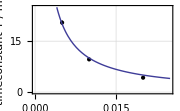
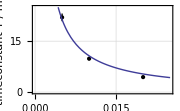
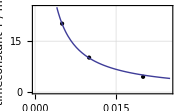
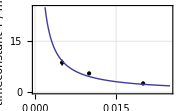

{{0.1004,0.0126858},{0.106813,0.0186293},{0.100504,0.00725181},{0.0459904,0.0142297}}

{0.101726,0.00369817}

```mathematica
densities={0.005,0.01,0.02};
fits={};
(
dat=Table[{densities⟦i⟧,#⟦i,1⟧,#⟦i,2⟧},{i,1,3}];
(fit=NonlinearModelFit[dat⟦1;;,1;;2⟧,a/x,{{a,0.1}},x]);
AppendTo[fits,fit];
Print[ToErrorForm/@fit["ParameterConfidenceIntervals"]];
Show[
ErrorListPlot[dat,PlotStyle->Black],
Plot[Normal@fit,{x,0,0.025},PlotRange->{0,25}],
Frame->True,Axes->None,GridLines->Automatic,PlotRange->{{0,0.025},{0,25}},ImageSize->Small,
FrameLabel->{"CuSO_4 density / M","timeconstant T / ms"}
])&/@{t2,t1se,t1mg,t1cp}
perD=(#⟦1⟧)&/@(ToErrorForm/@#["ParameterConfidenceIntervals"]&/@fits)
weightedMean[perD⟦1;;3⟧]
```